# General Cylinder Detector Calculation

Run this first

### Defining cylinder geometry and functions for computing event yield

In the form x,y,z (of the first cap centre), length, and radius. All in m. x is up, y is to the right, and z is down the beampipe

```mathematica
cylinderDef ={5,-5, 3,15,5, Pi/4,Pi/4} ;
cylinderDef2 ={-5,5, 3,15,5, -Pi/4,-Pi/4} ;
cylinderDef3 ={0,0, -7.08,15,5, Pi, 0} ;
```

#### Setting up cylinder definitions and relevant coordinate transformations

```mathematica
θfromη[η_]:=2 ArcCot[ⅇ^η];
ηfromθ[θ_]:=-Log[Tan[θ/2]];
```

Creates a parametric definition f(r,α) (cap
s) and f(l,α) (body). α runs from 0 to 2π while r and l are bounded by the input radius and length of the detector

```mathematica
cylinderAtOrigin[cylinderDef_]:={
{r*Sin[α], r*Cos[α], 0}
,
{r*Sin[α],r*Cos[α],cylinderDef[[4]]}
,
{cylinderDef[[5]]*Sin[α],cylinderDef[[5]]*Cos[α],l}
}

rotateCylinder[cylinderDef_] :=Transpose[RotationMatrix[cylinderDef[[6]],{0,1,0}].RotationMatrix[cylinderDef[[7]],{1,0,0}]. Transpose[ cylinderAtOrigin[cylinderDef] ] ]  

planeSegmentsFromCylinder[cylinderDef_]:={
{cylinderDef[[1]] + rotateCylinder[cylinderDef][[1]][[1]],cylinderDef[[2]]+rotateCylinder[cylinderDef][[1]][[2]],cylinderDef[[3]] +
 rotateCylinder[cylinderDef][[1]][[3]]}
,
{cylinderDef[[1]]+ rotateCylinder[cylinderDef][[2]][[1]],cylinderDef[[2]]+rotateCylinder[cylinderDef][[2]][[2]],cylinderDef[[3]] +
rotateCylinder[cylinderDef][[2]][[3]]}
,
{cylinderDef[[1]] + rotateCylinder[cylinderDef][[3]][[1]],cylinderDef[[2]]+ rotateCylinder[cylinderDef][[3]][[2]],cylinderDef[[3]]+
rotateCylinder[cylinderDef][[3]][[3]]}
}
EndCapsCylinder[cylinderDef_]:={
{cylinderDef[[1]] + rotateCylinder[cylinderDef][[1]][[1]],cylinderDef[[2]]+rotateCylinder[cylinderDef][[1]][[2]],cylinderDef[[3]] +
 rotateCylinder[cylinderDef][[1]][[3]]}
,
{cylinderDef[[1]]+ rotateCylinder[cylinderDef][[2]][[1]],cylinderDef[[2]]+rotateCylinder[cylinderDef][[2]][[2]],cylinderDef[[3]] +
rotateCylinder[cylinderDef][[2]][[3]]}
}
BaseCylinder[cylinderDef_]:={
{cylinderDef[[1]] + rotateCylinder[cylinderDef][[3]][[1]],cylinderDef[[2]]+ rotateCylinder[cylinderDef][[3]][[2]],cylinderDef[[3]]+
rotateCylinder[cylinderDef][[3]][[3]]}
}

planeSegmentsFromCylinder[cylinderDef] //MatrixForm
```

(5+1/2 r Cos[α]+(r Sin[α])/(√2) | -5+(r Cos[α])/(√2) | 3+1/2 r Cos[α]-(r Sin[α])/(√2)
25/2+1/2 r Cos[α]+(r Sin[α])/(√2) | -5-15/(√2)+(r Cos[α])/(√2) | 21/2+1/2 r Cos[α]-(r Sin[α])/(√2)
5+l/2+(5 Cos[α])/2+(5 Sin[α])/(√2) | -5-l/(√2)+(5 Cos[α])/(√2) | 3+l/2+(5 Cos[α])/2-(5 Sin[α])/(√2))

## Set up particle path geometry

```mathematica
xaxis={0,0,0}+s{1,0,0};
yaxis={0,0,0}+s{0,1,0};
zaxis={0,0,0}+s{0,0,1};
```

{1.,0}

{0.841471 s,0.,0.540302 s}

{}

{{ⅈ,ⅈ,ⅈ},{ⅈ,ⅈ,ⅈ}}

{ⅈ √3,ⅈ √3}

3D modeling of surface and ray interactions:

-Graphics3D-

estimate geometric coverage

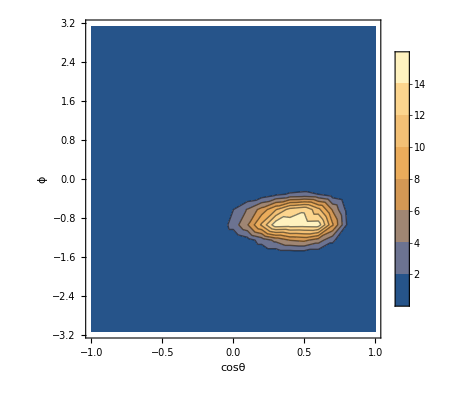

fraction of solid angle covered:

0.0675

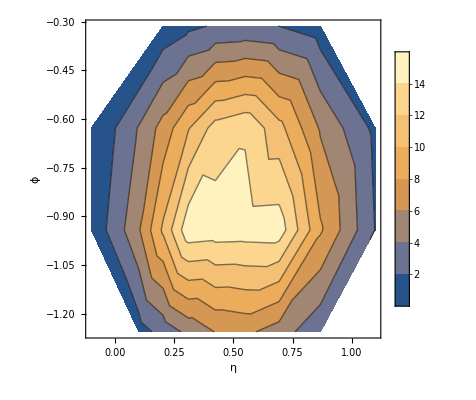

```mathematica
(*This sets the trajectory of the particle of interest that originates at the interaction point*)
{lineθ,lineϕ}={1.0,0}
currentline={0,0,0}+s{Sin[lineθ] Cos[lineϕ], Sin[lineθ] Sin[lineϕ],Cos[lineθ]}

(*This determines the intersections of a particle trajectory (currentline) and a detector determined by cylinder dfinition *)
intersectionCylinderSolutions=Select[
Flatten[Solve[Evaluate[currentline==#],{s,r,α,l}]&/@(planeSegmentsFromCylinder[cylinderDef])/.C[1]-> 0,1]
,((0≤ (r/.#)≤ cylinderDef[[5]]) && (s/.#)≥0 (*&& (α/.#)≥-3.1415*))||((0≤ (l/.#)≤ cylinderDef[[4]]) && (s/.#)≥0 )&]//Quiet

cylinderIntersectionPoints=If[Length[intersectionCylinderSolutions]>0,
Sort[currentline/.intersectionCylinderSolutions,#1.#1<#2.#2&]
,
{{ⅈ,ⅈ,ⅈ},{ⅈ,ⅈ,ⅈ}}
]

{√(cylinderIntersectionPoints[[1]].cylinderIntersectionPoints[[1]]),√(cylinderIntersectionPoints[[2]].cylinderIntersectionPoints[[2]])}

"3D modeling of surface and ray interactions:"
Show[
ParametricPlot3D[{
Evaluate[BaseCylinder[cylinderDef]]
},{α,0,2Pi},{l,0,cylinderDef[[4]]},
PlotRange->{{-1,1},{-1,1},{-1,1}}25,BoxRatios->{1,1,1},AxesLabel->{"x","y","z"},Mesh->False,
PlotStyle->Evaluate[Directive[#,Opacity[0.4]]&/@{Red,Red,Blue,Blue,Green,Green}]]
,
ParametricPlot3D[{
Evaluate[BaseCylinder[cylinderDef2]]
},{α,0,2Pi},{l,0,cylinderDef2[[4]]},
BoxRatios->{1,1,1},AxesLabel->{"x","y","z"},Mesh->False,
PlotStyle->Evaluate[Directive[#,Opacity[0.4]]&/@{Red,Red,Blue,Blue,Green,Green}]]
,
ParametricPlot3D[{
Evaluate[BaseCylinder[cylinderDef3]]
},{α,0,2Pi},{l,0,cylinderDef3[[4]]},
BoxRatios->{1,1,1},AxesLabel->{"x","y","z"},Mesh->False,
PlotStyle->Evaluate[Directive[#,Opacity[0.4]]&/@{Red,Red,Blue,Blue,Green,Green}]]
,
ParametricPlot3D[{
Evaluate[EndCapsCylinder[cylinderDef]]
},{α,0,2Pi},{r,0,cylinderDef[[5]]},
BoxRatios->{1,1,1},AxesLabel->{"x","y","z"},Mesh->False,
PlotStyle->Evaluate[Directive[#,Opacity[0.4]]&/@{Red,Red,Blue,Blue,Green,Green}]]
,
ParametricPlot3D[{
Evaluate[EndCapsCylinder[cylinderDef2]]
},{α,0,2Pi},{r,0,cylinderDef2[[5]]},
BoxRatios->{1,1,1},AxesLabel->{"x","y","z"},Mesh->False,
PlotStyle->Evaluate[Directive[#,Opacity[0.4]]&/@{Red,Red,Blue,Blue,Green,Green}]]
,
ParametricPlot3D[{
Evaluate[EndCapsCylinder[cylinderDef3]]
},{α,0,2Pi},{r,0,cylinderDef3[[5]]},
BoxRatios->{1,1,1},AxesLabel->{"x","y","z"},Mesh->False,
PlotStyle->Evaluate[Directive[#,Opacity[0.4]]&/@{Red,Red,Blue,Blue,Green,Green}]]
,
ParametricPlot3D[xaxis,{s,-1000,10000},BoxRatios->{1,1,1},AxesLabel->{"x","y","z"},PlotStyle->{Gray}]
,
ParametricPlot3D[yaxis,{s,-1000,10000},BoxRatios->{1,1,1},AxesLabel->{"x","y","z"},PlotStyle->{Gray}]
,
ParametricPlot3D[zaxis,{s,-1000,10000},BoxRatios->{1,1,1},AxesLabel->{"x","y","z"},PlotStyle->{Gray}]
]

"estimate geometric coverage"
L2mL1Cylasfncosθϕ=Flatten[Table[{cosθ,ϕ,

{lineθ,lineϕ}={ArcCos[cosθ],ϕ};
currentline={0,0,0}+s{Sin[lineθ] Cos[lineϕ], Sin[lineθ] Sin[lineϕ],Cos[lineθ]};

intersectionCylinderSolutions=Select[
Flatten[Solve[Evaluate[currentline==#],{s,r,α,l}]&/@(planeSegmentsFromCylinder[cylinderDef])/.C[1]-> 0,1]
,((0≤ (r/.#)≤ cylinderDef[[5]]) && (s/.#)≥0 )||((0≤ (l/.#)≤ cylinderDef[[4]]) && (s/.#)≥0 )&]//Quiet;

cylinderIntersectionPoints=If[Length[intersectionCylinderSolutions]>0,
Sort[currentline/.intersectionCylinderSolutions,#1.#1<#2.#2&]
,
{{ⅈ,ⅈ,ⅈ},{ⅈ,ⅈ,ⅈ}}
];

√(cylinderIntersectionPoints[[2]].cylinderIntersectionPoints[[2]])-√(cylinderIntersectionPoints[[1]].cylinderIntersectionPoints[[1]])
}
,{cosθ,1,-1,-0.1},{ϕ,-π,π,π/10}],1];

ListContourPlot[L2mL1Cylasfncosθϕ,PlotLegends->Automatic, FrameLabel->{"cosθ","ϕ"}]


"fraction of solid angle covered:"
1/(4π)(Transpose[Select[L2mL1Cylasfncosθϕ,#[[3]]>0&]][[1]]//Max[#]-Min[#]&)(Transpose[Select[L2mL1Cylasfncosθϕ,#[[3]]>0&]][[2]]//Max[#]-Min[#]&)


ListContourPlot[{ArcCos[#[[1]]]//ηfromθ,#[[2]],#[[3]]}&/@Select[L2mL1Cylasfncosθϕ,#[[3]]>0&],PlotLegends->Automatic, FrameLabel->{"η","ϕ"}]
```

## Define particle entry and exit points and setting up event yield

```mathematica
DecayProb[L1_?NumericQ,L2_?NumericQ,bλ_?NumericQ]:=ⅇ^(-L1/bλ)-ⅇ^(-L2/bλ);
```

CylinderDetectorL1L2m takes in the cylinder definition and defining variables of a a particle trajectory, θ and ϕ. From these, it determines the intercept points L1 and L2 and outputs their radial distance from the interaction point. Trajectories with no intersection return complex values.

```mathematica
CylinderDetectorL1L2m[θ_,ϕ_,cylinderDef_]:=Module[{cosθ},
cosθ=Cos[θ];
{lineθ,lineϕ}={ArcCos[cosθ],ϕ};
currentline={0,0,0}+s{Sin[lineθ] Cos[lineϕ], Sin[lineθ] Sin[lineϕ],Cos[lineθ]};

intersectionCylinderSolutions=Select[
Flatten[Solve[Evaluate[currentline==#],{s,r,α,l}]&/@(planeSegmentsFromCylinder[cylinderDef])/.C[1]-> 0,1]
,((0≤ (r/.#)≤ cylinderDef[[5]]) && (s/.#)≥0 (*&& (α/.#)≥-3.1415*))||((0≤ (l/.#)≤ cylinderDef[[4]]) && (s/.#)≥0 )&]//Quiet;

cylinderIntersectionPoints=If[Length[intersectionCylinderSolutions]>0,
Sort[currentline/.intersectionCylinderSolutions,#1.#1<#2.#2&]
,
{1/(√3){ⅈ,ⅈ,ⅈ},1/(√3){ⅈ,ⅈ,ⅈ}}
];

{√(cylinderIntersectionPoints[[1]].cylinderIntersectionPoints[[1]]),√(cylinderIntersectionPoints[[2]].cylinderIntersectionPoints[[2]])}
];
```

As the name implies, this function determines the values of Cos θ and ϕ that lead to trajectories that reach the detector. The interior table creates a list of values for each angular coordinate pair that has the form {Cos θ, ϕ, distance travelled in the detector}. If the angular coordinates do not lead to an intersecting trajectory, the value of the third entry is set to 0. The final several lines convert this information into a range of angular values {Cos θ min, Cos θ max}, {ϕ min, ϕ max} while making certain that we don’t extend beyond the coordinate limits due to the addition of the variable steps.

```mathematica
Findcosθϕrange[cylinderDef_,cosθstep_:2/20,ϕstep_:2π/20]:=Module[{},
L2mL1Cylasfncosθϕ=Flatten[Table[{cosθ,ϕ,

{lineθ,lineϕ}={ArcCos[cosθ],ϕ};
currentline={0,0,0}+s{Sin[lineθ] Cos[lineϕ], Sin[lineθ] Sin[lineϕ],Cos[lineθ]};

intersectionCylinderSolutions=Select[
Flatten[Solve[Evaluate[currentline==#],{s,r,α,l}]&/@(planeSegmentsFromCylinder[cylinderDef])/.C[1]-> 0,1]
,((0≤ (r/.#)≤ cylinderDef[[5]]) && (s/.#)≥0 )||((0≤ (l/.#)≤ cylinderDef[[4]]) && (s/.#)≥0 )&]//Quiet;

cylinderIntersectionPoints=If[Length[intersectionCylinderSolutions]>0,
Sort[currentline/.intersectionCylinderSolutions,#1.#1<#2.#2&]
,
{{ⅈ,ⅈ,ⅈ},{ⅈ,ⅈ,ⅈ}}
];

√(cylinderIntersectionPoints[[2]].cylinderIntersectionPoints[[2]])-√(cylinderIntersectionPoints[[1]].cylinderIntersectionPoints[[1]])
}
,{cosθ,1,-1,-cosθstep},{ϕ,-π,π,ϕstep}],1];


preRange ={(Transpose[Select[L2mL1Cylasfncosθϕ,#[[3]]>0&]][[1]]//{Min[#]-cosθstep,Max[#]+cosθstep}&)
,(Transpose[Select[L2mL1Cylasfncosθϕ,#[[3]]>0&]][[2]]//{Min[#]-ϕstep,Max[#]+ϕstep}&)
};

range ={{If[preRange[[1]][[1]]<-1,-1,preRange[[1]][[1]]],If[preRange[[1]][[2]]>1,1,preRange[[1]][[2]]]},{If[preRange[[2]][[1]]<-Pi,-Pi,preRange[[2]][[1]]],If[preRange[[2]][[2]]>Pi,Pi,preRange[[2]][[2]]]}}

];
```

```mathematica
(*Findcosθϕrange[cylinderDef] Test to ensure this is working as planned*)
```

```mathematica
ComputeDecayEfficiencyCylinderDetector[θblist_, currentcτmeters_, cylinderDef_,currentcosθϕrange_]:=Module[{θblistflat},
θblistflat=Flatten[θblist,1];
(*we choose ϕ randomly to lie within the range covered by the box detector, and weigh accordingly*)
(*(this would obviously not be ok if we wanted to detect two particles per event, since the ϕ correlations have been thrown out, but doesn't matter for us)*)
(currentcosθϕrange[[2]][[2]]-currentcosθϕrange[[2]][[1]])/(2π)( Sum[
X1=θblistflat[[i]];
PX1inCyl=(DecayProb[#1⟦1⟧,#1⟦2⟧,currentcτmeters X1⟦2⟧]&)[CylinderDetectorL1L2m[X1⟦1⟧,RandomReal[currentcosθϕrange[[2]]],cylinderDef]];
{PX1inCyl,PX1inCyl^2}
,{i,1,Length[θblistflat]}]
//{#[[1]],√(#[[2]])}&
)/Length[θblist]//Re
]
```

From the below  functions, it appears that the .dat files are organized in scattering events that have a certain number dark pions (points). The three terms of the points within each entry are θ, ϕ, and the boost factor (I think).

```mathematica
(*This routine computes the point of entry and exit for each particle, along the line of motion.*)
L1L2[event_]:=
Table[
CylinderDetectorL1L2m[point[[1]],point[[2]],cylinderDef]~Join~{point[[3]]}
,{point,event}];
```

```mathematica
(*This routine computes the probability of at least one and at least 2 vertices in the detector. The inputs is are the list of (entrypoint,exitpoints) for each event, obtained with the previous routine, as well as the lifetime.*)
EventProb[event_,logcτ_]:=(Module[{problist},
problist=Re[DecayProb[#[[1]],#[[2]],#[[3]]*10^logcτ]]&/@event;
{1-(Times@@(1-problist)),
1-(Times@@(1-problist))-Sum[Times@@(ReplacePart[#,i->1-#[[i]]]&@(1-problist)),{i,Length[problist]}]}
])
```

## Format empty cells:

```mathematica
NotebookDelete/@Select[Cells[GeneratedCell->False],StringMatchQ[First@FrontEndExecute[FrontEnd`ExportPacket[NotebookRead@#,"InputText"]],(" "|"\t"|"\r"|"\n"|"
")...]&]
```

{}